# Expression of S_22^(↑↑;T) (S_22^(↓↓;T)) and S_22^(↑↓;T) (S_22^(↓↑;T))in helical edge modes, Eq. (10) of SM. At zero temperature, the Fermi-Dirac distributions are replaces by the appropriate Heaviside theta function, which gives Eq. (8) of SM.

```mathematica
ρ=√(1-Subscript[T, 0]);
τ=√Subscript[T, 0];
(*θ=ArcTan[ρ/τ];*)
θ=0;
ξ=α-θ;
α=0;
p=0;
χ1=χ2=0;
s1={{0,-I √p Exp[I*ξ],τ √(1-p)Exp[I*α],0,0,0,-I ρ √(1-p)Exp[I*α],0},{-I √p,0,0,0,0,0,0,√(1-p)Exp[I χ1]},{0,0,0,-I √p,√(1-p)Exp[I χ2],0,0,0},{0,τ √(1-p)Exp[-I*α],-I √p Exp[-I*ξ],0,0,I ρ √(1-p)Exp[-I*α],0,0},{0,0,-I ρ √(1-p)Exp[I*α],0,0,-I √p Exp[I*ξ],τ √(1-p)Exp[I*α],0},{0,0,0,√(1-p)Exp[-I χ2],-I √p,0,0,0},{√(1-p)Exp[-I χ1],0,0,0,0,0,0,-I √p},{0,I ρ √(1-p)Exp[-I*α],0,0,0,τ √(1-p)Exp[-I*α],-I √p Exp[-I*ξ],0}};
```

```mathematica
Subscript[f, 1]=Subscript[f, 2]=SubPlus[f];
Subscript[f, 3]=Subscript[f, 4]=SubMinus[f];
Subscript[f, 5]=Subscript[f, 6]=SubMinus[f];
Subscript[f, 7]=Subscript[f, 8]=SubPlus[f];
```

```mathematica
S22uu=Sum[((KroneckerDelta[3,γ]KroneckerDelta[3,λ]-Conjugate[Part[s1,3,γ]]Part[s1,3,λ])(KroneckerDelta[3,λ]KroneckerDelta[3,γ]-Conjugate[Part[s1,3,λ]]Part[s1,3,γ]))*(Subscript[f, γ][G](1-Subscript[f, λ][G+ω])+Subscript[f, λ][G+ω](1-Subscript[f, γ][G])),{γ,1,8},{λ,1,8}]
S22dd=Sum[((KroneckerDelta[4,γ]KroneckerDelta[4,λ]-Conjugate[Part[s1,4,γ]]Part[s1,4,λ])(KroneckerDelta[4,λ]KroneckerDelta[4,γ]-Conjugate[Part[s1,4,λ]]Part[s1,4,γ]))*(Subscript[f, γ][G](1-Subscript[f, λ][G+ω])+Subscript[f, λ][G+ω](1-Subscript[f, γ][G])),{γ,1,8},{λ,1,8}]
```

2 f_-[G] (1-f_-[G+ω])+2 (1-f_-[G]) f_-[G+ω]

f_-[G] (1-f_-[G+ω])+(1-f_-[G]) f_-[G+ω]+Conjugate[√(1-T_0)]^2 (1-T_0) (f_-[G] (1-f_-[G+ω])+(1-f_-[G]) f_-[G+ω])+Conjugate[√(1-T_0)] Conjugate[√T_0] √(1-T_0) √T_0 (f_-[G+ω] (1-f_+[G])+(1-f_-[G+ω]) f_+[G])+Conjugate[√(1-T_0)] Conjugate[√T_0] √(1-T_0) √T_0 (f_-[G] (1-f_+[G+ω])+(1-f_-[G]) f_+[G+ω])+Conjugate[√T_0]^2 T_0 (f_+[G] (1-f_+[G+ω])+(1-f_+[G]) f_+[G+ω])

```mathematica
S22ud=Sum[((KroneckerDelta[3,γ]KroneckerDelta[3,λ]-Conjugate[Part[s1,3,γ]]Part[s1,3,λ])(KroneckerDelta[4,λ]KroneckerDelta[4,γ]-Conjugate[Part[s1,4,λ]]Part[s1,4,γ]))*(Subscript[f, γ][G](1-Subscript[f, λ][G+ω])+Subscript[f, λ][G+ω](1-Subscript[f, γ][G])),{γ,1,8},{λ,1,8}]
S22du=Sum[((KroneckerDelta[4,γ]KroneckerDelta[4,λ]-Conjugate[Part[s1,4,γ]]Part[s1,4,λ])(KroneckerDelta[3,λ]KroneckerDelta[3,γ]-Conjugate[Part[s1,3,λ]]Part[s1,3,γ]))*(Subscript[f, γ][G](1-Subscript[f, λ][G+ω])+Subscript[f, λ][G+ω](1-Subscript[f, γ][G])),{γ,1,8},{λ,1,8}]
```

0

0

# Expression of S_11^(↑↑;T) (S_11^(↓↓;T)) and S_11^(↑↓;T) (S_11^(↓↑;T))in trivial edge modes, Eq. (15) of SM. At zero temperature, the Fermi-Dirac distributions are replaces by the appropriate Heaviside theta function, which gives Eq. (14) of SM.

```mathematica
ρ=√(1-Subscript[T, 0]);
τ=√Subscript[T, 0];
(*θ=ArcTan[ρ/τ];*)
θ=0;
ξ=α-θ;
α=0;
χ1=χ2=0;
s1={{0,-I √Subscript[P, 0] Exp[I*ξ],τ √(1-Subscript[P, 0])Exp[I*α],0,0,0,-I ρ √(1-Subscript[P, 0])Exp[I*α],0},{-I √Subscript[P, 0],0,0,0,0,0,0,√(1-Subscript[P, 0])Exp[I χ1]},{0,0,0,-I √Subscript[P, 0],√(1-Subscript[P, 0])Exp[I χ2],0,0,0},{0,τ √(1-Subscript[P, 0])Exp[-I*α],-I √Subscript[P, 0] Exp[-I*ξ],0,0,I ρ √(1-Subscript[P, 0])Exp[-I*α],0,0},{0,0,-I ρ √(1-Subscript[P, 0])Exp[I*α],0,0,-I √Subscript[P, 0] Exp[I*ξ],τ √(1-Subscript[P, 0])Exp[I*α],0},{0,0,0,√(1-Subscript[P, 0])Exp[-I χ2],-I √Subscript[P, 0],0,0,0},{√(1-Subscript[P, 0])Exp[-I χ1],0,0,0,0,0,0,-I √Subscript[P, 0]},{0,I ρ √(1-Subscript[P, 0])Exp[-I*α],0,0,0,τ √(1-Subscript[P, 0])Exp[-I*α],-I √Subscript[P, 0] Exp[-I*ξ],0}};
```

```mathematica
Subscript[f, 1]=Subscript[f, 2]=SubPlus[f];
Subscript[f, 3]=Subscript[f, 4]=SubMinus[f];
Subscript[f, 5]=Subscript[f, 6]=SubPlus[f];
Subscript[f, 7]=Subscript[f, 8]=SubMinus[f];
```

```mathematica
S11uu=Sum[((KroneckerDelta[1,γ]KroneckerDelta[1,λ]-Conjugate[Part[s1,1,γ]]Part[s1,1,λ])(KroneckerDelta[1,λ]KroneckerDelta[1,γ]-Conjugate[Part[s1,1,λ]]Part[s1,1,γ]))*(Subscript[f, γ][G](1-Subscript[f, λ][G+ω])+Subscript[f, λ][G+ω](1-Subscript[f, γ][G])),{γ,1,8},{λ,1,8}]
S11dd=Sum[((KroneckerDelta[2,γ]KroneckerDelta[2,λ]-Conjugate[Part[s1,2,γ]]Part[s1,2,λ])(KroneckerDelta[2,λ]KroneckerDelta[2,γ]-Conjugate[Part[s1,2,λ]]Part[s1,2,γ]))*(Subscript[f, γ][G](1-Subscript[f, λ][G+ω])+Subscript[f, λ][G+ω](1-Subscript[f, γ][G])),{γ,1,8},{λ,1,8}]
```

Conjugate[√(1-P_0) √(1-T_0)]^2 (1-P_0) (1-T_0) (f_-[G] (1-f_-[G+ω])+(1-f_-[G]) f_-[G+ω])+2 Conjugate[√(1-P_0) √(1-T_0)] Conjugate[√(1-P_0) √T_0] (1-P_0) √(1-T_0) √T_0 (f_-[G] (1-f_-[G+ω])+(1-f_-[G]) f_-[G+ω])+Conjugate[√(1-P_0) √T_0]^2 (1-P_0) T_0 (f_-[G] (1-f_-[G+ω])+(1-f_-[G]) f_-[G+ω])+Conjugate[√P_0] Conjugate[√(1-P_0) √(1-T_0)] √(1-P_0) √P_0 √(1-T_0) (f_-[G+ω] (1-f_+[G])+(1-f_-[G+ω]) f_+[G])+Conjugate[√P_0] Conjugate[√(1-P_0) √T_0] √(1-P_0) √P_0 √T_0 (f_-[G+ω] (1-f_+[G])+(1-f_-[G+ω]) f_+[G])+f_+[G] (1-f_+[G+ω])+(1-f_+[G]) f_+[G+ω]+Conjugate[√P_0] Conjugate[√(1-P_0) √(1-T_0)] √(1-P_0) √P_0 √(1-T_0) (f_-[G] (1-f_+[G+ω])+(1-f_-[G]) f_+[G+ω])+Conjugate[√P_0] Conjugate[√(1-P_0) √T_0] √(1-P_0) √P_0 √T_0 (f_-[G] (1-f_+[G+ω])+(1-f_-[G]) f_+[G+ω])+Conjugate[√P_0]^2 P_0 (f_+[G] (1-f_+[G+ω])+(1-f_+[G]) f_+[G+ω])

Conjugate[√(1-P_0)]^2 (1-P_0) (f_-[G] (1-f_-[G+ω])+(1-f_-[G]) f_-[G+ω])+Conjugate[√(1-P_0)] Conjugate[√P_0] √(1-P_0) √P_0 (f_-[G+ω] (1-f_+[G])+(1-f_-[G+ω]) f_+[G])+f_+[G] (1-f_+[G+ω])+(1-f_+[G]) f_+[G+ω]+Conjugate[√(1-P_0)] Conjugate[√P_0] √(1-P_0) √P_0 (f_-[G] (1-f_+[G+ω])+(1-f_-[G]) f_+[G+ω])+Conjugate[√P_0]^2 P_0 (f_+[G] (1-f_+[G+ω])+(1-f_+[G]) f_+[G+ω])

```mathematica
S11ud=Sum[((KroneckerDelta[1,γ]KroneckerDelta[1,λ]-Conjugate[Part[s1,1,γ]]Part[s1,1,λ])(KroneckerDelta[2,λ]KroneckerDelta[2,γ]-Conjugate[Part[s1,2,λ]]Part[s1,2,γ]))*(Subscript[f, γ][G](1-Subscript[f, λ][G+ω])+Subscript[f, λ][G+ω](1-Subscript[f, γ][G])),{γ,1,8},{λ,1,8}]
S11du=Sum[((KroneckerDelta[2,γ]KroneckerDelta[2,λ]-Conjugate[Part[s1,2,γ]]Part[s1,2,λ])(KroneckerDelta[1,λ]KroneckerDelta[1,γ]-Conjugate[Part[s1,1,λ]]Part[s1,1,γ]))*(Subscript[f, γ][G](1-Subscript[f, λ][G+ω])+Subscript[f, λ][G+ω](1-Subscript[f, γ][G])),{γ,1,8},{λ,1,8}]
```

-2 Conjugate[√P_0] √P_0 (f_+[G] (1-f_+[G+ω])+(1-f_+[G]) f_+[G+ω])

-2 Conjugate[√P_0] √P_0 (f_+[G] (1-f_+[G+ω])+(1-f_+[G]) f_+[G+ω])

# Expression of colored Δ_T noise

```mathematica
f1[G_,ω_,x_]:=1/(1+Exp[(G+ω*10)/(1+x/2)]);
f2[G_,ω_,x_]:=1/(1+Exp[(G+ω*10)/(1-x/2)]);
D1[ω_?NumericQ,x_?NumericQ]:=0.25NIntegrate[(f2[G,0,x]-f1[G,0,x])(f2[G,ω,x]-f1[G,ω,x]),{G,-∞,∞}]
```

# Fig. 2(a) of paper

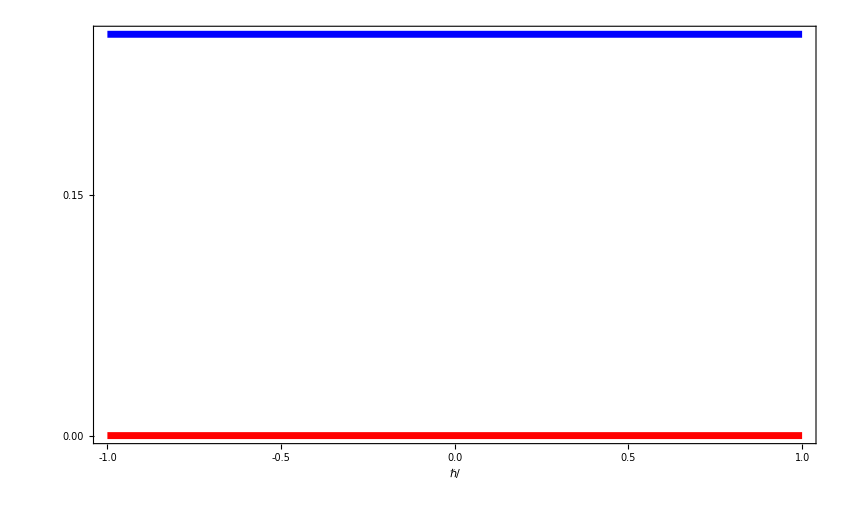

```mathematica
A1=Plot[{0,(1)0.5*0.5},{ω,-1,1},PlotRange->{{-1,1},{0.3,-0.02}},Exclusions->None,AxesOrigin->{0.0,-0.02},PlotStyle->{{Red,AbsoluteThickness[5]},{Blue,AbsoluteThickness[5]},{Brown,AbsoluteThickness[5]},{Yellow,AbsoluteThickness[5]}},FrameLabel->{Style["ℏ/",45,Bold,Black],Style[Rotate["",270 Degree],45,Black]},FrameStyle->Directive[Black,Thickness[0.002]],FrameTicks->{{{{0.15,"0.15"},{0.30,"0.30"},{0,"0.00"}},None},{{{1,"1.0"},{0.5,"0.5"},{0,"0.0"},{-0.5,"-0.5"},{-1,"-1.0"}},None}},FrameTicksStyle->Directive["Label",Black,45],ImageSize->850,Frame->True]
```

```mathematica
A2=Legended[Plot[{0,D1[ω,0.1]},{ω,-1,1},PlotRange->{{-1,1},{0.0006,-0.0003}},Exclusions->None,AxesOrigin->{0.0,0.0000},PlotStyle->{{Red,AbsoluteThickness[5]},{Blue,AbsoluteThickness[5]},{Brown,AbsoluteThickness[5]},{Yellow,AbsoluteThickness[5]}},PlotLegends->Placed[{Style["",55,Black],Style["",55,Black]},{Right,Top}],FrameLabel->{Style["ℏ/",55,Bold,Black],Style[Rotate["",270 Degree],55,Black]},FrameStyle->Directive[Black,Thickness[0.002]],FrameTicks->{{{{0.0006,"0.60"},{0.0003,"0.30"},{0,"0.00"},{-0.0003,"-0.30"}},None},{{{1,"1.0"},{0.5,"0.5"},{0,"0.0"},{-0.5,"-0.5"},{-1,"-1.0"}},None}},FrameTicksStyle->Directive["Label",Black,55],ImageSize->1700,Frame->True,Epilog->{Transparent,EdgeForm[{Pink,Thick}],Inset[A1,Scaled[{0.35,0.95}],Scaled[{0.35,0.95}],1.10],PlotRange->{0.2,0.3},PlotRangeClipping->False}],{Placed[Style["× 10^-3",55,Black],{{0.25,1.0}}]}]
```

-Graphics-

# Fig. 2(b) of paper

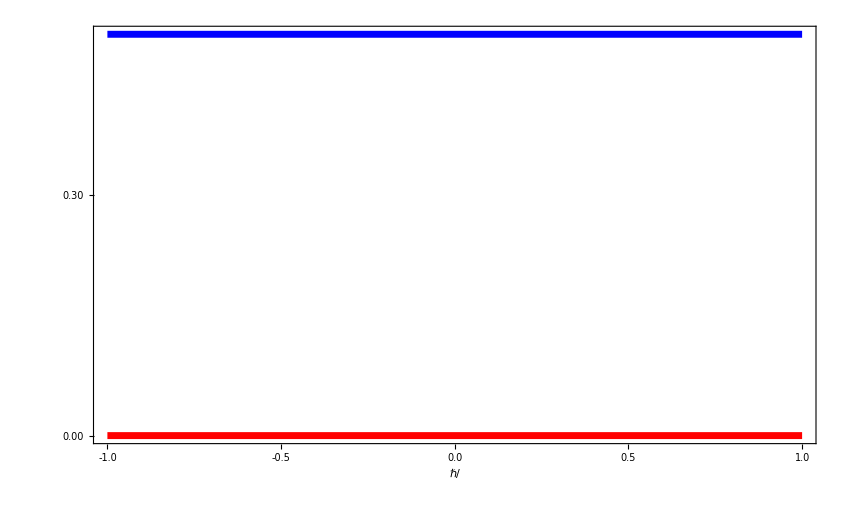

```mathematica
A1=Plot[{0,(2)0.5*0.5},{ω,-1,1},PlotRange->{{-1,1},{0.6,-0.02}},Exclusions->None,AxesOrigin->{0.0,-0.02},PlotStyle->{{Red,AbsoluteThickness[5]},{Blue,AbsoluteThickness[5]},{Brown,AbsoluteThickness[5]},{Yellow,AbsoluteThickness[5]}},FrameLabel->{Style["ℏ/",45,Bold,Black],Style[Rotate["",270 Degree],45,Black]},FrameStyle->Directive[Black,Thickness[0.002]],FrameTicks->{{{{0.60,"0.60"},{0.30,"0.30"},{0,"0.00"}},None},{{{1,"1.0"},{0.5,"0.5"},{0,"0.0"},{-0.5,"-0.5"},{-1.00,"-1.0"}},None}},FrameTicksStyle->Directive["Label",Black,45],ImageSize->850,Frame->True]
```

```mathematica
A2=Legended[Plot[{0,2D1[ω,0.1]},{ω,-1,1},PlotRange->{{-1,1},{0.0012,-0.0006}},Exclusions->None,AxesOrigin->{0.0,0.0000},PlotStyle->{{Red,AbsoluteThickness[5]},{Blue,AbsoluteThickness[5]},{Brown,AbsoluteThickness[5]},{Yellow,AbsoluteThickness[5]}},PlotLegends->Placed[{Style["",55,Black],Style["",55,Black]},{Right,Top}],FrameLabel->{Style["ℏ/",55,Bold,Black],Style[Rotate["",270 Degree],55,Black]},FrameStyle->Directive[Black,Thickness[0.002]],FrameTicks->{{{{0.0012,"1.20"},{0.0006,"0.60"},{0,"0.00"},{-0.0006,"-0.60"}},None},{{{1,"1.0"},{0.5,"0.5"},{0,"0.0"},{-0.5,"-0.5"},{-1,"-1.0"}},None}},FrameTicksStyle->Directive["Label",Black,55],ImageSize->1700,Frame->True,Epilog->{Transparent,EdgeForm[{Pink,Thick}],Inset[A1,Scaled[{0.35,0.95}],Scaled[{0.35,0.95}],1.10],PlotRange->{0.2,0.3},PlotRangeClipping->False}],{Placed[Style["× 10^-3",55,Black],{{0.25,1.0}}]}]
```

-Graphics-

# Fig. 2(a) of Supplemental Material

```mathematica
A1=Legended[Plot[{0,D1[0,x],D1[0.5,x],D1[1,x]},{x,0,0.1},PlotRange->{{0,0.1},{0.0006,-0.00002}},Exclusions->None,AxesOrigin->{0.0,-0.00002},PlotStyle->{{Red,AbsoluteThickness[5]},{Blue,AbsoluteThickness[5]},{Brown,AbsoluteThickness[5]},{Green,AbsoluteThickness[5]}},PlotLegends->Placed[{Style["",45],Style["ℏ",45],Style["ℏ",45],Style["ℏ",45]},{Left,Top}],FrameLabel->{Style["",45,Bold,Black],Style[Rotate["",270 Degree],45,Black]},FrameStyle->Directive[Black,Thickness[0.002]],FrameTicks->{{{{0.0006,"0.60"},{0.0003,"0.30"},{0,"0.00"}},None},{{{0.1,"0.10"},{0.05,"0.05"},{0,"0.00"}},None}},FrameTicksStyle->Directive["Label",Black,45],ImageSize->1500,Frame->True],{Placed[Style["× 10^-3",45,Black],{{0.22,1.0}}]}]
```

-Graphics-

# Fig. 2(b) of Supplemental Material

```mathematica
A1=Legended[Plot[{0,2D1[0,x],2D1[0.5,x],2D1[1,x]},{x,0,0.1},PlotRange->{{0,0.1},{0.0012,-0.00002}},Exclusions->None,AxesOrigin->{0.0,-0.00002},PlotStyle->{{Red,AbsoluteThickness[5]},{Blue,AbsoluteThickness[5]},{Brown,AbsoluteThickness[5]},{Green,AbsoluteThickness[5]}},PlotLegends->Placed[{Style["",45],Style["ℏ",45],Style["ℏ",45],Style["ℏ",45]},{Left,Top}],FrameLabel->{Style["",45,Bold,Black],Style[Rotate["",270 Degree],45,Black]},FrameStyle->Directive[Black,Thickness[0.002]],FrameTicks->{{{{0.0006,"0.60"},{0.0012,"1.20"},{0,"0.00"}},None},{{{0.1,"0.10"},{0.05,"0.05"},{0,"0.00"}},None}},FrameTicksStyle->Directive["Label",Black,45],ImageSize->1500,Frame->True],{Placed[Style["× 10^-3",45,Black],{{0.22,1.0}}]}]
```

-Graphics-

# Fig. 3 of Supplemental Material

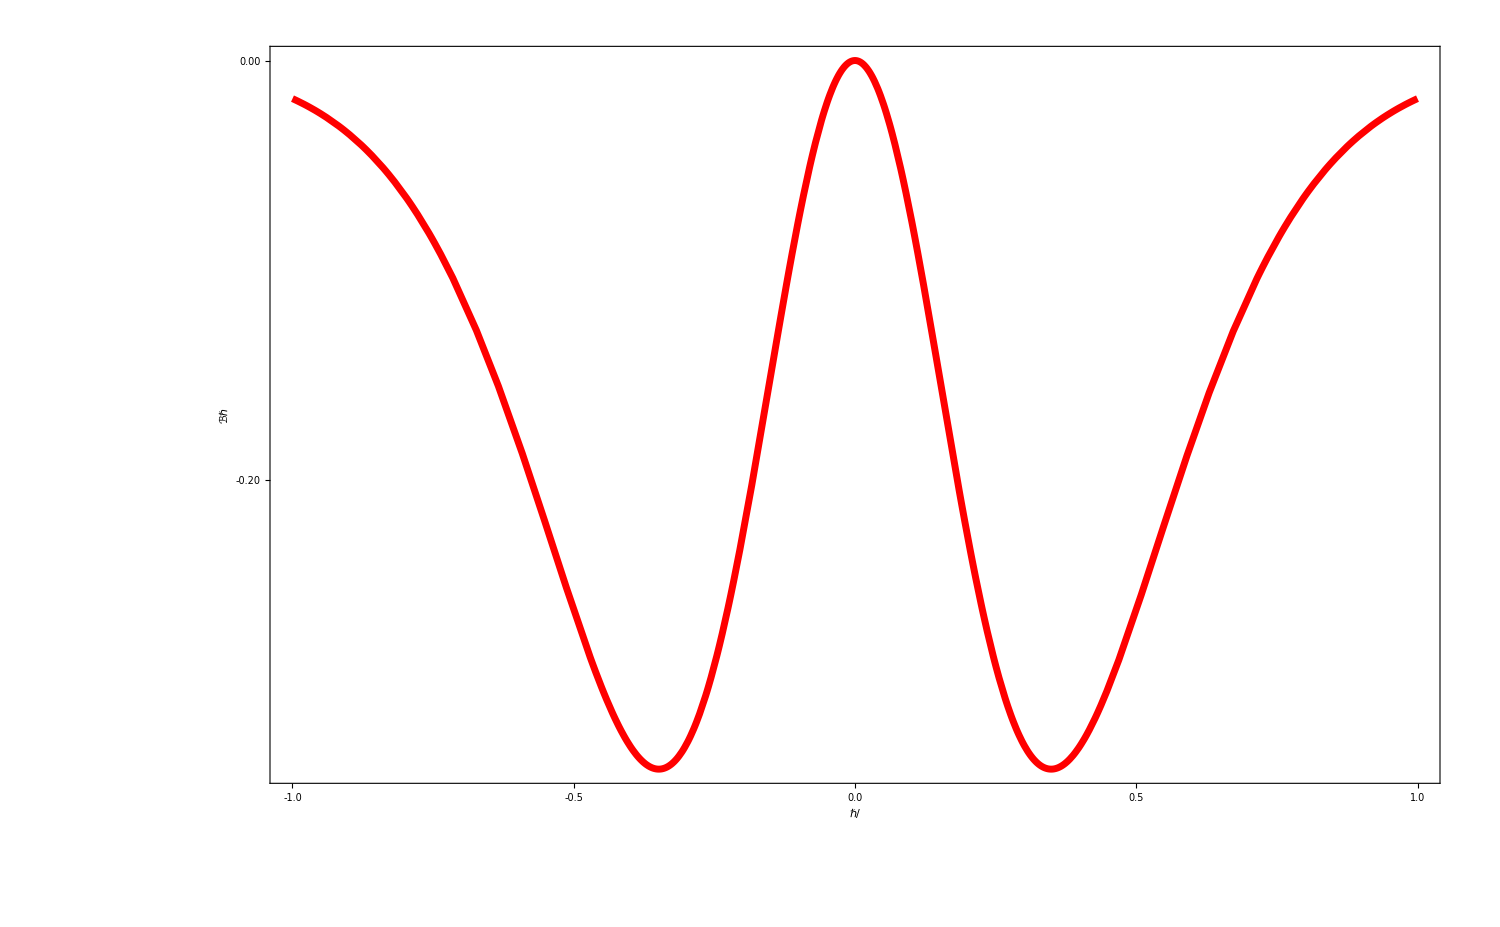

```mathematica
a=x*10;
A1=Plot[Exp[a]/(6(Exp[a]-1)^3)(2(π^2-E^a π^2+6 (-1+E^a) PolyLog[2,-E^-a]+6 (-1+E^a) PolyLog[2,-E^a]+6 PolyLog[3,-E^-a]+6 E^a PolyLog[3,-E^-a]-6 PolyLog[3,-E^a]-6 E^a PolyLog[3,-E^a])),{x,-1,1},PlotRange->{{-1,1},{0,0.3}},Exclusions->None,AxesOrigin->{0.0,0.0000},PlotStyle->{{Blue,AbsoluteThickness[5]}},FrameLabel->{Style["ℏ/",35,Bold,Black],Style[Rotate["𝒜",270 Degree],35,Black]},FrameStyle->Directive[Black,Thickness[0.002]],FrameTicks->{{{{0.15,"0.15"},{0.3,"0.30"},{0,"0.00"}},None},{{{-1,"-1.0"},{-0.5,"-0.5"},{0,"0.0"},{0.5,"0.5"},{1,"1.0"}},None}},FrameTicksStyle->Directive["Label",Black,35],ImageSize->750,Frame->True];
A2=Plot[Exp[a]/(6(Exp[a]-1)^3)((π^2+E^a π^2+6 Log[1+E^-a]-6 E^a Log[1+E^-a]-6 Log[1+E^a]+6 E^a Log[1+E^a]+6 (1+E^a) PolyLog[2,-E^-a]+6 (1+E^a) PolyLog[2,-E^a])*a ),{x,-1,1},PlotRange->{{-1,1},{0,-0.4}},Exclusions->None,AxesOrigin->{0.0,0.0000},PlotStyle->{{Red,AbsoluteThickness[5]}},FrameLabel->{Style["ℏ/",45,Bold,Black],Style[Rotate["ℬℏ",270 Degree],45,Black]},FrameStyle->Directive[Black,Thickness[0.002]],FrameTicks->{{{{-0.2,"-0.20"},{-0.4,"-0.40"},{0,"0.00"}},None},{{{-1,"-1.0"},{-0.5,"-0.5"},{0,"0.0"},{0.5,"0.5"},{1,"1.0"}},None}},FrameTicksStyle->Directive["Label",Black,45],ImageSize->1500,Frame->True,Epilog->{Transparent,EdgeForm[{Pink,Thick}],Inset[A1,Scaled[{0.25,0.95}],Scaled[{0.25,0.95}],0.95],PlotRange->{0.2,0.3},PlotRangeClipping->False}]
```